# RandomWalk2D Report

## Eamon O’Connor Alec Ramos

## Given start, lower and upper. What is the probability that the walk hits upper before it hits lower?

### 1. Data collection

```mathematica
(*Returns the final point of a random walk which starts at (0,start) and stops when the y coordinate of a point reaches one of the inpu bounds*)
stopPointRandomWalk[lower_, upper_, start_]:= Module[
{y = start,counter = 0, ListOfPoints = List[], x= 0},
While[y≠ upper && y ≠  lower,
(*Add a point to the walk as long as y is within bounds*)
AppendTo[ListOfPoints, {x,y}];
x++;
y= y+RandomChoice[{-1,1}];
];
AppendTo[ListOfPoints,{x,y}];
(*Return last point in the walk*)
Return[Last[ListOfPoints]]
]
```

```mathematica
countStopOfStopRandomWalk[lower_,upper_,start_,iterations_]:= Module[{sum=List[],i=1,lowerCount=0,upperCount=0},
While[i≤iterations,AppendTo[sum,stopPointRandomWalk[lower,upper,start]];i++];
sum = Flatten[Take[sum,All,{2}]];

lowerCount= Count[sum,lower];
upperCount= Count[sum,upper];
Return[{lowerCount,upperCount}]
]
```

```mathematica
lst={};
```

```mathematica
For[i = 0,i≤15,i++,AppendTo[lst,countStopOfStopRandomWalk[-2,i,0,10000]]]
```

```mathematica
lst
```

{{0,10000},{3326,6674},{4988,5012},{6001,3999},{6654,3346},{7139,2861},{7499,2501},{7705,2295},{8033,1967},{8142,1858},{8274,1726},{8496,1504},{8516,1484},{8664,1336},{8751,1249},{8768,1232}}

```mathematica
lst2={};
```

```mathematica
For[i = 0,i≤15,i++,AppendTo[lst2,countStopOfStopRandomWalk[-3,i,0,10000]]]
```

```mathematica
lst2
```

{{0,10000},{2408,7592},{3945,6055},{4993,5007},{5683,4317},{6298,3702},{6684,3316},{7004,2996},{7404,2596},{7524,2476},{7701,2299},{7920,2080},{7960,2040},{8180,1820},{8232,1768},{8254,1746}}

```mathematica
lst3={};
```

```mathematica
For[i = 0,i≤15,i++,AppendTo[lst3,countStopOfStopRandomWalk[-4,i,0,10000]]]
```

```mathematica
lst3
```

{{0,10000},{1955,8045},{3329,6671},{4325,5675},{4952,5048},{5571,4429},{6008,3992},{6375,3625},{6695,3305},{6922,3078},{7115,2885},{7377,2623},{7433,2567},{7572,2428},{7753,2247},{7884,2116}}

### 2. Graph

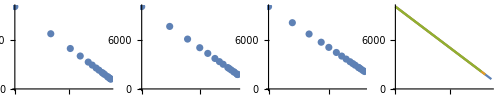

```mathematica
GraphicsGrid[{{ListPlot[lst],ListPlot[lst2],ListPlot[lst3],ListLinePlot[{lst,lst2,lst3}]}}]
```

### 3. Conjectures/observation

(i) the data looks like the line y = -x
(ii) it does not look as linear when the upper is close to start that is due to less iterations of the random function when they are closer.
(iii) In ListLinePlot you can see that as lower is higher the line gets closer to touching 0 when upper = 15

### 4.Fitting the data

```mathematica
Fit[lst, {1,x},x]
Fit[lst2, {1,x},x]
Fit[lst3, {1,x},x]
```

10000.-1. x

10000.-1. x

10000.-1. x

the pattern here has become very obvious

#### 5.Results

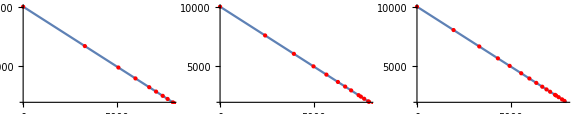

```mathematica
GraphicsGrid[{{
Show[Plot[10000.000000000013-1.000000000000001 x,{x,0,8000}],ListPlot[lst,PlotStyle->{PointSize[Large],Red}]],Show[Plot[10000.000000000013-1.000000000000001 x,{x,0,8000}],ListPlot[lst2,PlotStyle->{PointSize[Large],Red}]],
Show[Plot[10000.000000000013-1.000000000000001 x,{x,0,8000}],ListPlot[lst3,PlotStyle->{PointSize[Large],Red}]]
}}]
```

### Final Conjecture:

The relationship between the distance from upper-start and stopRandomWalk[] is linear.

## Given lower and upper: What is the average length of a path that starts in the middle of the interval and reaches the boundary of the interval?

### Context/preliminary observation:

I think it will be similar to the one before this but instead the equation will be y=x

### 1.Data Collection

```mathematica
lstb={};
```

```mathematica
For[i = 0,i≥-15,i--,AppendTo[lstb,countStopOfStopRandomWalk[i,2,0,10000]]]
```

```mathematica
lstb
```

{{10000,0},{6629,3371},{5038,4962},{4087,5913},{3364,6636},{2835,7165},{2481,7519},{2180,7820},{1978,8022},{1813,8187},{1625,8375},{1534,8466},{1362,8638},{1292,8708},{1201,8799},{1150,8850}}

```mathematica
lstb2={};
```

```mathematica
For[i = 0,i≥-15,i--,AppendTo[lstb2,countStopOfStopRandomWalk[i,2,0,10000]]]
```

```mathematica
lstb2
```

{{10000,0},{6703,3297},{4957,5043},{4003,5997},{3433,6567},{2890,7110},{2549,7451},{2248,7752},{1925,8075},{1866,8134},{1717,8283},{1538,8462},{1387,8613},{1282,8718},{1222,8778},{1189,8811}}

```mathematica
lstb3={};
```

```mathematica
For[i = 0,i≥-15,i--,AppendTo[lstb3,countStopOfStopRandomWalk[i,2,0,10000]]]
```

```mathematica
lstb3
```

{{10000,0},{6680,3320},{5062,4938},{4005,5995},{3421,6579},{2875,7125},{2412,7588},{2255,7745},{1993,8007},{1801,8199},{1624,8376},{1552,8448},{1420,8580},{1323,8677},{1199,8801},{1145,8855}}

### 2. Visual representation

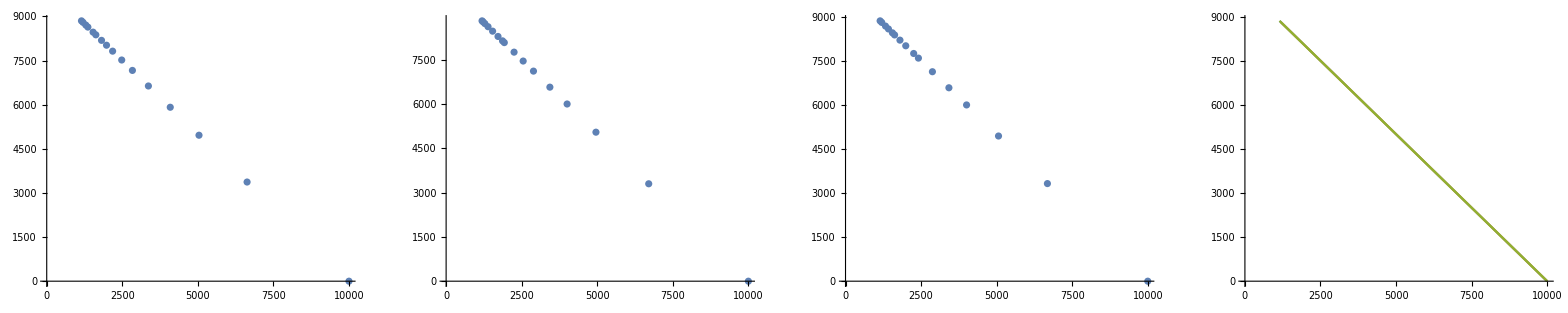

```mathematica
GraphicsGrid[{{ListPlot[lstb],ListPlot[lstb2],ListPlot[lstb3],ListLinePlot[{lstb,lstb2,lstb3}]}}]
```

### 3. Conjectures/Observation

(i) the data looks like the line y = -x (not as i anticipated)
(ii) it does not look as linear when the lower is close to start that is due to less iterations of the random function when they are closer.
  (iii) In ListLinePlot you can see that when lower is higher the line gets father from touching 0 when upper = -15

### 4. Fitting the data

```mathematica
Fit[lstb, {1,x},x]
Fit[lstb2, {1,x},x]
Fit[lstb3, {1,x},x]
```

10000.-1. x

10000.-1. x

10000.-1. x

another obvious pattern

### 5. Results

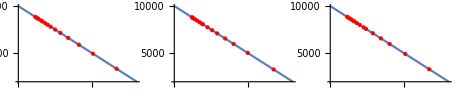

```mathematica
GraphicsGrid[{{
Show[Plot[10000.000000000013-1.000000000000001 x,{x,0,8000}],ListPlot[lstb,PlotStyle->{PointSize[Large],Red}]],Show[Plot[10000.000000000013-1.000000000000001 x,{x,0,8000}],ListPlot[lstb2,PlotStyle->{PointSize[Large],Red}]],
Show[Plot[10000.000000000013-1.000000000000001 x,{x,0,8000}],ListPlot[lstb3,PlotStyle->{PointSize[Large],Red}]]}}]
```

### Final Conjecture

The relationship between the distance from |lower| and stopRandomWalk[] is linear.

## Can You predict the average length of random walk when you increment both lower and upper bounds?

### Context/preliminary observation:

this time i don’t believe the line will be linear

### 1.Data Collection

```mathematica
avgLengthRandomWalk[lower_,upper_,start_,iterations_]:= Module[{sum=0,i=1},While[i≤iterations,sum+=lengthRandomWalk[lower,upper,start];i++];
Return[N[sum/iterations]]
]
```

```mathematica
lengthRandomWalk[lower_, upper_, start_]:= Module[
{y = start,counter = 0, ListOfPoints = List[], x= 0},
While[y< upper && y > lower,
(*Append points to the list until one of the bounds is reached.*)
AppendTo[ListOfPoints, {x,y}];
x++;
y= y+RandomChoice[{-1,1}];
];
(*Append the final point*)
AppendTo[ListOfPoints,{x,y}];
(*Return length of walk*)
Return[Length[ListOfPoints]-1]
]
```

```mathematica
data={};
```

```mathematica
For[i=1,i≤10,i++,AppendTo[data,{i,avgLengthRandomWalk[-i,i,0,10000]}]]
```

```mathematica
data
```

{{1,1.},{2,4.0202},{3,8.9918},{4,16.068},{5,25.072},{6,35.9396},{7,49.1722},{8,63.5152},{9,81.8122},{10,99.2224}}

### 2. Visual representation

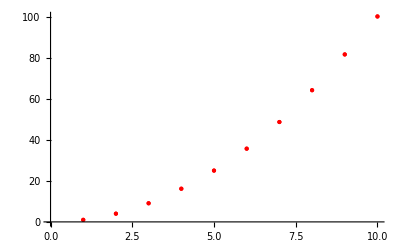

```mathematica
Show[ListPlot[data,PlotStyle ->  Directive[Red, PointSize[Large]]]]
```

### 3. Conjectures/Observation

This line looks a lot like the line y=x^2

### 4. Fitting the data

```mathematica
Fit[data, {1,x,x^2},x]
```

-0.169633+0.114285 x+0.987595 x^2

```mathematica
Fit[data, {x,x^2},x]
```

0.0499062 x+0.992705 x^2

```mathematica
Fit[data, {x^2},x]
```

0.998664 x^2

I took out the constant and then the x coefficient because they were so little it is basically zero

### 5. Results

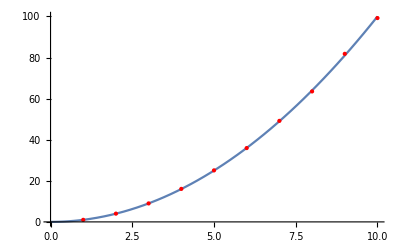

```mathematica
Show[Plot[{x^2},{x,0,10}],ListPlot[data,PlotStyle ->  Directive[Red, PointSize[Large]]]]
```

### Final Conjecture

When you increment the bounds the length of random walk goes up exponentially. The equation for this is y=x^2

# ModRandomWalk2D Report

## Eamon O’Connor Alec Ramos

## Suppose we choose probability p for staying at the same location. How does the length differ when using different bounds?

## 1.Data Collection

```mathematica
(*Outputs the final point of a modStopRandomWalk*)
modStopPointRandomWalk[lower_, upper_, probToStay_, start_]:= Module[
{PointList = List[{0, start}], count = 1, y = start, x = 0, RealNum},
While[1>0,
RealNum = RandomReal[];
(*first, check if the point is staying at the same y coordinate*)
If[0≤ RealNum < probToStay,
x++;
AppendTo[PointList, {x, y}],
(*now, check if the point is at one of the bounds*)
If[Last[Last[PointList]] == upper || Last[Last[PointList]] == lower,
(*Return the final point if a bound is reached*)
Return[Last[PointList]],
x++;
y = y+ RandomChoice[{-1,1}];
AppendTo[PointList, {x,y}]
]
];
count++
];
]
```

```mathematica
(*For a modRandom walk starting at (0,start) whose y coordinate never leaves the interval [lower, upper], and stops when the bound is reached, outputs the list of points*)
modStopRandomWalk[lower_, upper_, probToStay_, start_]:= Module[
{PointList = List[{0, start}], count = 1, y = start, x = 0, RealNum},
While[1>0,
RealNum = RandomReal[];
(*first, check if the point is staying at the same y coordinate*)
If[0≤ RealNum < probToStay,
x++;
AppendTo[PointList, {x, y}],
(*now, check if the point is at one of the bounds*)
(*Last[Last[PointList]] is probably the same as Last[PointList][[2]]*)
If[Last[Last[PointList]] == upper || Last[Last[PointList]] == lower,

Return[{Show[ListPlot[PointList, PlotStyle -> Red], ListLinePlot[PointList]],PointList}],
x++;
y = y+ RandomChoice[{-1,1}];
(*Append the new point to the list*)
AppendTo[PointList, {x,y}]
]
];
count++
];

]
```

```mathematica
countStopOfModStopRandomWalk[lower_,upper_,probToStay_,start_,iterations_]:= Module[{sum=List[],i=1,lowerCount=0,upperCount=0},
While[i≤iterations,AppendTo[sum,modStopPointRandomWalk[lower,upper,probToStay,start]];i++];
sum = Flatten[Take[sum,All,{2}]];

lowerCount= Count[sum,lower];
upperCount= Count[sum,upper];
Return[{lowerCount,upperCount}]
]
```

```mathematica
lst={};
```

```mathematica
For[i = 0,i≤8,i++,AppendTo[lst,countStopOfModStopRandomWalk[-2,i,.33,0,
10000]]]
```

```mathematica
lst
```

{{0,10000},{3308,6692},{5018,4982},{5975,4025},{6676,3324},{7160,2840},{7547,2453},{7810,2190},{7989,2011}}

```mathematica
lst2={};
```

```mathematica
For[i = 0,i≤8,i++,AppendTo[lst2,countStopOfModStopRandomWalk[-3,i,0.33,0,10000]]]
```

```mathematica
lst2
```

{{0,10000},{2530,7470},{4009,5991},{5073,4927},{5715,4285},{6304,3696},{6664,3336},{6971,3029},{7233,2767}}

```mathematica
lst3={};
```

```mathematica
For[i = 0,i≤8,i++,AppendTo[lst3,countStopOfModStopRandomWalk[-4,i,0.33,0,10000]]]
```

```mathematica
lst3
```

{{0,10000},{2021,7979},{3392,6608},{4333,5667},{5017,4983},{5584,4416},{6057,3943},{6359,3641},{6663,3337}}

## 2. Visual representation

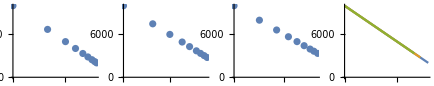

```mathematica
GraphicsGrid[{{ListPlot[lst],ListPlot[lst2],ListPlot[lst3],ListLinePlot[{lst,lst2,lst3}]}}]
```

## 3. Conjectures/Observation

(i) the data looks like the line y = -x
(ii) it does not look as linear when the upper is close to start that is due to less iterations of the random function when they are closer.
(iii) In ListLinePlot you can see that as upper is higher it is more likely to hit lower

## 4. Fitting the data

```mathematica
Fit[lst, {1,x},x]
Fit[lst2, {1,x},x]
Fit[lst3, {1,x},x]
```

10000.-1. x

10000.-1. x

10000.-1. x

the pattern here has become very obvious

## 5. Results

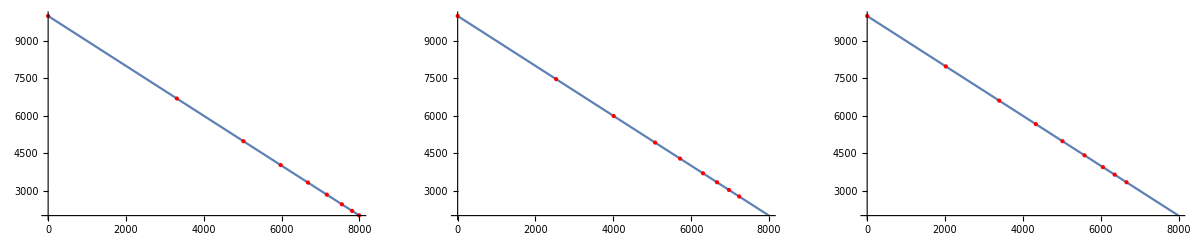

```mathematica
GraphicsGrid[{{
Show[Plot[10000.000000000013-1.000000000000001 x,{x,0,8000}],ListPlot[lst,PlotStyle->{PointSize[Large],Red}]],Show[Plot[10000.000000000013-1.000000000000001 x,{x,0,8000}],ListPlot[lst2,PlotStyle->{PointSize[Large],Red}]],
Show[Plot[10000.000000000013-1.000000000000001 x,{x,0,8000}],ListPlot[lst3,PlotStyle->{PointSize[Large],Red}]]
}}]
```

## Final Conjecture

The relationship between the distance from upper-start and ModstopRandomWalk[] is linear.

## Given Upper and lower how does the graph change based on change in probability of staying?

## 1.Data Collection

```mathematica
lstP={};
```

```mathematica
For[i = 0,i<10,i++,AppendTo[lstP,countStopOfModStopRandomWalk[-5,5,(i/10),0,
10000]]]
```

```mathematica
lstP
```

{{4924,5076},{4968,5032},{5038,4962},{4989,5011},{4955,5045},{5035,4965},{4953,5047},{4939,5061},{4952,5048},{5067,4933}}

```mathematica
lstP2={};
```

```mathematica
For[i = 0,i<10,i++,AppendTo[lstP2,countStopOfModStopRandomWalk[-2,2,(i/10),0,
10000]]]
```

```mathematica
lstP2
```

{{4973,5027},{4958,5042},{4974,5026},{4993,5007},{4996,5004},{4955,5045},{4996,5004},{4979,5021},{5035,4965},{5014,4986}}

```mathematica
lstP3={};
```

```mathematica
For[i = 0,i<10,i++,AppendTo[lstP3,countStopOfModStopRandomWalk[-7,7,(i/10),0,
10000]]]
```

```mathematica
lstP3
```

{{5023,4977},{5071,4929},{5107,4893},{4954,5046},{5017,4983},{5008,4992},{4950,5050},{5021,4979},{5005,4995},{4934,5066}}

## 2. Visual representation

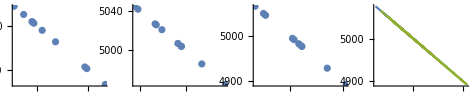

```mathematica
GraphicsGrid[{{ListPlot[lstP],ListPlot[lstP2],ListPlot[lstP3],ListLinePlot[{lstP,lstP2,lstP3}]}}]
```

## 3. Conjectures/Observation

(i)Although the data looks straight its actually a cluster that is very close together.

(ii)i believe the equation from this graph i Y=X

## 4. Fitting the data

```mathematica
Fit[lstP, {1,x},x]
Fit[lstP2, {1,x},x]
Fit[lstP3, {1,x},x]
```

10000.-1. x

10000.-1. x

10000.-1. x

This is not what i was expecting but it is an easy equation to understand

## 5. Results

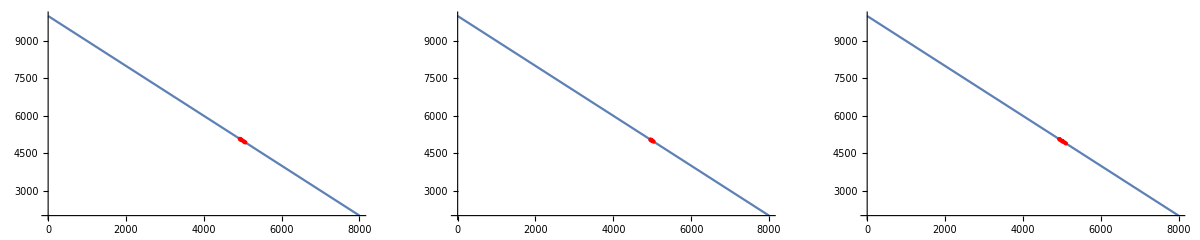

```mathematica
GraphicsGrid[{{
Show[Plot[10000.000000000013-1.000000000000001 x,{x,0,8000}],ListPlot[lstP,PlotStyle->{PointSize[Large],Red}]],Show[Plot[10000.000000000013-1.000000000000001 x,{x,0,8000}],ListPlot[lstP2,PlotStyle->{PointSize[Large],Red}]],
Show[Plot[10000.000000000013-1.000000000000001 x,{x,0,8000}],ListPlot[lstP3,PlotStyle->{PointSize[Large],Red}]]
}}]
```

## Final Conjecture

From this last graph we can more easily see what is going on. It appears to be Y=X but once inside of the cluster the equation for the points is 10000- x=Y

## How does the probability of hiting upper differ when we increase upper and increase lower but also increase probability of staying?

## 1.Data Collection

```mathematica
lstC={};
```

```mathematica
For[i = 0,i<5,i++,AppendTo[lstC,countStopOfModStopRandomWalk[-5+i,5+i,(i/10),0,
10000]]]
```

```mathematica
lstC
```

{{5063,4937},{6052,3948},{7003,2997},{8013,1987},{9050,950}}

```mathematica
lstC2={};
```

```mathematica
For[i = 0,i<8,i++,AppendTo[lstC2,countStopOfModStopRandomWalk[-9+i,9+i,(i/10),0,
10000]]]
```

```mathematica
lstC2
```

{{4960,5040},{5593,4407},{6075,3925},{6667,3333},{7275,2725},{7713,2287},{8336,1664},{8845,1155}}

## 2. Visual representation

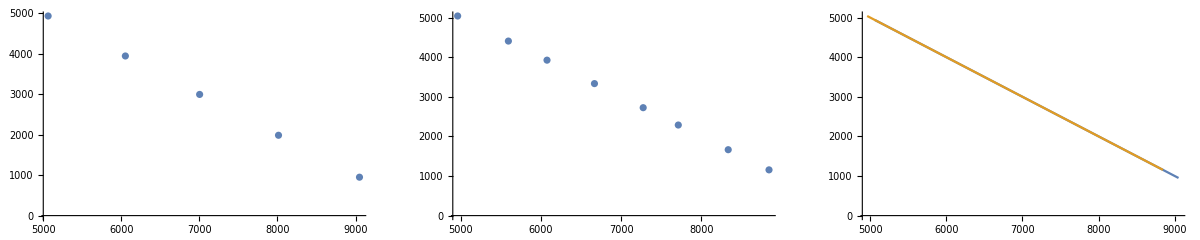

```mathematica
GraphicsGrid[{{ListPlot[lstC],ListPlot[lstC2],ListLinePlot[{lstC,lstC2}]}}]
```

## 3. Conjectures/Observation

(i) the data looks like the line y = -x

(ii) In ListLinePlot you can see that as lower is higher it is more likely to hit lower

## 4. Fitting the data

```mathematica
Fit[lstC, {1,x},x]
Fit[lstC2, {1,x},x]
```

10000.-1. x

10000.-1. x

## 5. Results

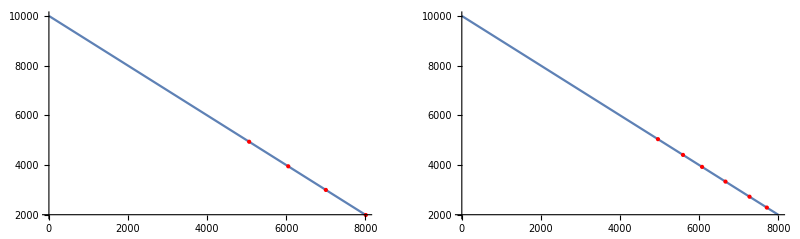

```mathematica
GraphicsGrid[{{
Show[Plot[10000.000000000013-1.000000000000001 x,{x,0,8000}],ListPlot[lstC,PlotStyle->{PointSize[Large],Red}]],Show[Plot[10000.000000000013-1.000000000000001 x,{x,0,8000}],ListPlot[lstC2,PlotStyle->{PointSize[Large],Red}]]
}}]
```

## Final Conjecture

As upper and lower are incremented it is more likely to hit lower.

# RandomWalk3D Report

## Eamon O’Connor Alec Ramos

## Given Y and Z: what is the boundary to corner ratio?

## 1.Data Collection

```mathematica
stopPointRandomWalk3D[lower_, upper_, start_]:= Module[
{x = 0, y, z, lowerY =lower[[1]],lowerZ= lower[[2]],upperY = upper[[1]], upperZ = upper[[2]],  ListOfPoints=List[], startPoint3D},

y = start[[1]];
z = start[[2]];
startPoint3D = {0, y, z};
While[(y≠  upperY &&y≠ lowerY && z ≠  upperZ&& z ≠  lowerZ),
(*we append here so that we start by appending the starting point to the list*)
AppendTo[ListOfPoints, {x, y, z}];
x++;

y= y+RandomChoice[{-1,1}];


z= z+RandomChoice[{-1,1}];
];
AppendTo[ListOfPoints, {x,y,z}];
(*fix the parameters of the Show function*)
Return[Last[ListOfPoints]];

]
```

```mathematica
lowerUpper3D[lower_, upper_, start_, repeat_]:= Module[
{iterations = 1, upperY = 0, lowerY = 0, upperZ = 0, lowerZ = 0,corner = 0, res = {}, a, cornerCheck = 0},
While[iterations ≤ repeat,
a=stopPointRandomWalk3D[lower, upper, start];
cornerCheck = 0;
If[a[[2]] == lower[[1]],
lowerY++;
cornerCheck++;
];
If[a[[2]] == upper[[1]],
upperY++;
cornerCheck++;
];
If[a[[3]] == lower[[2]],
lowerZ++;
cornerCheck++;
];
If[a[[3]] == upper[[2]],
upperZ++;
cornerCheck++;
];

If[cornerCheck == 2,
corner++;
];
iterations++;
];

res = {lowerY, upperY, lowerZ, upperZ, corner};
Return[res]

]
```

```mathematica
lowerUpper3D[{-10,-10},{10,10},{0,0},10000]
```

{2487,2488,2584,2541,100}

```mathematica
averageBoundry=(2487+2488+2584+2541)/4
```

2525

## 2. Visual representation

```mathematica
PieChart[{2525,100}]
```

-Graphics-

## 3. Conjectures/Observation

```mathematica
N@100/2525
```

0.039604

## Final Conjecture

About 4% of the time when upper and lower are equally far away from start it will hit a corner

## If the upper and lower are not equally far away will this percent change?

## 1.Data Collection

upper is twice as far

```mathematica
lowerUpper3D[{-10,-10},{20,20},{0,0},10000]
```

{3828,1212,3765,1238,43}

```mathematica
averageBoundry=(3828+1212+3765+1238)/4
```

```mathematica
N@(10043/4)
```

2510.75

upper is 3 times as far

```mathematica
lowerUpper3D[{-10,-10},{30,30},{0,0},10000]
```

{4299,737,4302,701,39}

```mathematica
averageBoundry=(4299+737+4302+701)/4
```

```mathematica
N@(10039/4)
```

2509.75

upper is 4 times as far

```mathematica
lowerUpper3D[{-10,-10},{40,40},{0,0},10000]
```

{4546,419,4613,456,34}

```mathematica
averageBoundry=(4546+419+4613+456)/4
```

```mathematica
N@(5017/2)
```

2508.5

## 2. Visual representation

```mathematica
GraphicsGrid[{{PieChart[{2510.75,43}],PieChart[{2509.75,43}],PieChart[{2508.5,34}]}}]
```

-Graphics-

```mathematica
40/2510
```

```mathematica
N@(4/251)
```

0.0159363

## 3. Conjectures/Observation

```mathematica
40/2510
```

```mathematica
N@(4/251)
```

0.0159363

it appears all the charts are similar and about 1.5% of the pie chart is blue

## Final Conjecture

there is a drastic change between equal and not equal then after that the difference is a lot smaller and the corners take up about 1.5%

## As the boundries grow farther how do the y and z values compare?

## 1.Data Collection

```mathematica
lowerUpper3D[{-10,-10},{10,10},{0,0},10000]
```

{2487,2488,2584,2541,100}

```mathematica
lowerUpper3D[{-10,-10},{20,20},{0,0},10000]
```

{3828,1212,3765,1238,43}

```mathematica
lowerUpper3D[{-10,-10},{30,30},{0,0},10000]
```

{4299,737,4302,701,39}

```mathematica
lowerUpper3D[{-10,-10},{40,40},{0,0},10000]
```

{4546,419,4613,456,34}

```mathematica
lowerUpper3D[{-10,-10},{50,50},{0,0},10000]
```

{4737,310,4667,309,23}

## 2. Visual representation

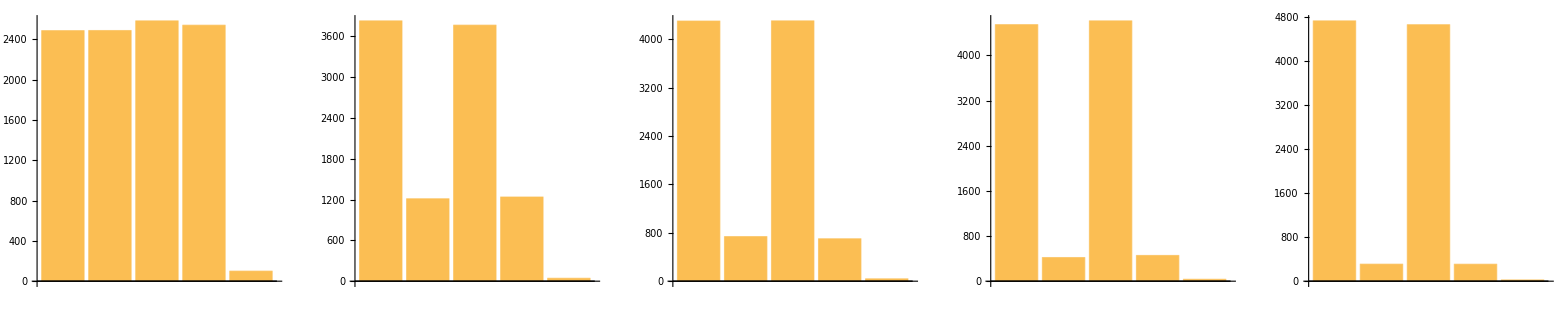

```mathematica
GraphicsGrid[{{BarChart[{2487,2488,2584,2541,100}],BarChart[{3828,1212,3765,1238,43}],BarChart[{4299,737,4302,701,39}],BarChart[{4546,419,4613,456,34}],BarChart[{4737,310,4667,309,23}]}}]
```

Left to right the labels are
{lowerY, upperY, lowerZ, upperZ, corner}

## 3. Conjectures/Observation

As the upper boundaries grow farther the bars become lower

## Final Conjecture

As the upper boundaries grow farther the likelihood of hitting both the boundaries and hitting a corner goes down.

### Computational problem

#### Tracing functions with text

```mathematica
a
```

```mathematica
(*creates list of points given a function, bounds, and the number of points that you want*)
createPointLst[func_, lower_, upper_, points_]:=Module[
{xspace=(upper-lower)/(points-1)},
Table[{x, func[x]}, {x,lower, upper, xspace}]
]
```

```mathematica
f[x_]:=x^2
```

```mathematica
createPointLst[f, 0, 5, 5]
```

{{0,0},{5/4,25/16},{5/2,25/4},{15/4,225/16},{5,25}}

```mathematica
h[x_]:=Sin[x]
```

```mathematica
createPointLst[h, 0, 2π, 10]
```

{{0,0},{(2 π)/9,Sin[(2 π)/9]},{(4 π)/9,Cos[π/18]},{(2 π)/3,(√3)/2},{(8 π)/9,Sin[π/9]},{(10 π)/9,-Sin[π/9]},{(4 π)/3,-(√3)/2},{(14 π)/9,-Cos[π/18]},{(16 π)/9,-Sin[(2 π)/9]},{2 π,0}}

```mathematica
(*splits up string into each letter and the point it needs to be at*)
prepareTextDisplay[text_, ptLst_, color_]:=Module[
{cnt=1, list},
Table[
(*Text is needed to plot later*)
Text[Style[StringTake[text, {cnt}], Large, color], ptLst[[cnt]]],
{cnt, StringLength@text}
]
]
```

```mathematica
ptLst ={{0,0},{0.3, 0},{0.6,0.2},{1.2,0.9},{1.5, 0.3}, {2, -.8}, {2.5, -1.9}};
```

```mathematica
newlist=prepareTextDisplay["Gatton",ptLst, Green]
```

{Text[G,{0,0}],Text[a,{0.3,0}],Text[t,{0.6,0.2}],Text[t,{1.2,0.9}],Text[o,{1.5,0.3}],Text[n,{2,-0.8}]}

```mathematica
FullForm[newlist[[1]]]
```

Text[Style["G",Large,RGBColor[0,1,0]],List[0,0]]

```mathematica
ptLst2={{1,1}, {2,2}, {3,3}, {4,4}, {5,5}, {6,6}};
newlist2=prepareTextDisplay["Linear", ptLst2, Green]
```

{Text[L,{1,1}],Text[i,{2,2}],Text[n,{3,3}],Text[e,{4,4}],Text[a,{5,5}],Text[r,{6,6}]}

```mathematica
(*displays information from primitive list in preareTextDisplay*)
displayText[primitiveLst_]:=
Graphics[primitiveLst]
```

```mathematica
displayText[newlist]
```

-Graphics-

```mathematica
displayText[newlist2]
```

-Graphics-

```mathematica
(*plots function with the letters from the function*)
horizontalTrace[func_, text_, lower_, upper_, color_]:=Module[{pointlist},
pointlist=createPointLst[func, lower, upper, StringLength[text]];
Show[Plot[func[x], {x, lower, upper}, PlotRange->All], 
(*display letter list*)
displayText[prepareTextDisplay[text, pointlist, color]], PlotRange->All 
]
]
```

```mathematica
g[x_]:=E^-x Sin[x]
```

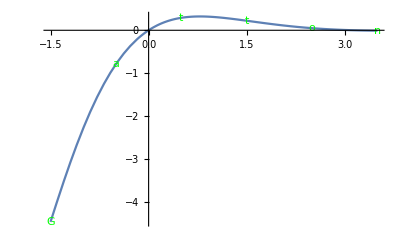

```mathematica
horizontalTrace[g, "Gatton", -1.5, 3.5, Green]
```

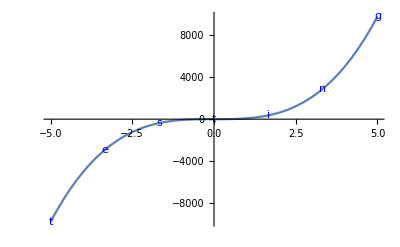

```mathematica
z[x_]:=78 x^3+3x-1
horizontalTrace[z, "testing", -5, 5, Blue]
```

```mathematica
b
```

```mathematica
(*finds number of spaces each line needs to reflect the y value of a func*)
createSpaceLst[func_,lower_, upper_,lines_, maxBlanks_]:=Module[
(*gets points from creatPointList funtion*)
{pointList=createPointLst[func, lower, upper, lines],yList},
yList=Table[{pointList[[cnt, 2]]}, {cnt, Length@pointList}];
(*the equation is a proportion of the y corrdinate to the maxBlanks, and scales accordingly such that the maximum number of spaces is maxBlanks*)
Flatten@Table[Round[(yList[[pt]]-Min[yList])/(Max[yList]-Min[yList])*maxBlanks], {pt, Length@yList}]
]
```

```mathematica
gv[x_]:=0.5 x^2
```

```mathematica
createSpaceLst[gv, -1.5, 3, 8, 10]
```

{2,1,0,0,1,3,6,10}

```mathematica
hv[x_]:=Cos[4x]
createSpaceLst[hv, 0, π/2,8, 7]
```

{7,6,2,0,0,2,6,7}

```mathematica
(*prints text after offset characters*)
offsetPrint[offset_,character_,text_]:=Module[
{str="", i=1},
While[i≤offset,
(*concatenates character*)
str=str<>character;
i++];
(*concatenates text*)
str=str<>text;
Print[str]
]
```

```mathematica
offsetPrint[5, " ", "Please give me an A"]
```

Please give me an A

```mathematica
offsetPrint[7, "@", "Hello"]
```

@@@@@@@Hello

```mathematica
(*is passed a list of spaces and prints the text out after each space element*)
verticalTrace[func_, text_, lines_, lower_, upper_, maxBlanks_]:=Module[{yList=createSpaceLst[func, lower, upper, lines, maxBlanks], cnt=1},
While[cnt≤lines,
offsetPrint[yList[[cnt]], " ", text];
cnt++
]
]
```

```mathematica
verticalTrace[gv, "Parabola", 8, -1.5, 3, 10]
```

Parabola

Parabola

Parabola

«5 more identical outputs»

```mathematica
ty[x_]:=x^3
```

```mathematica
verticalTrace[ty, "cubic", 6, -10, 10, 7]
```

cubic

cubic

cubic

«3 more identical outputs»